## Initialisation stuff

```mathematica
Needs["QDENSITY`Qdensity`"];
packageDir =FileNameJoin[{ NotebookDirectory[],"QSIM"}];
Needs["QSIM`noise`",FileNameJoin[{packageDir,"QSIM_noise.m"}]]
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

```mathematica
?QDENSITY`Qdensity`*
```

```mathematica
ExpmFidelity[Op1_,Op2_]:=Fidelity[Op1,Op2]^2;
CombineErrors[errorTable_]:=Module[{x,probNone},probNone=Times@@((1-#)&/@errorTable);
Total[Table[probNone errorTable[[ii]]/(1-errorTable[[ii]]),{ii,1,Length[errorTable]}]]](*for small probabilities, these depolarizing channels just add up.*)
PZ[i_]:=Switch[i,0,Subscript[𝒫, 0],1,Subscript[𝒫, 1]];
projectors={PX,PY,PZ};
KP[r__]:=KroneckerProduct[r];
phi0={{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}};
id =𝕀;
bellState[i_]:=ArrayFlatten[Outer[Times,PauliMatrix[i],PauliMatrix[0]]].phi0.ArrayFlatten[Outer[Times,PauliMatrix[i],PauliMatrix[0]]];
Fidelity
```

Fidelity

#### Single qubit gates

```mathematica
(*Definition of single spin rotations using the qdensity package
Nomenclature:  r followed by a capital letter --> rotation by π around the axis specified by the letter.
			r followed by a lower case letter: rotation by π/2 around the axis specified by that letter
The rotation direction is given by the appended letter m or p*)

{rxp,rXp,ryp,rYp,rzp,rZp}=Table[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))],{j,1,6}];
```

#### Data functions

```mathematica
findFileInDataDir[string_,dataDir_,daysPreviousToSearch_:365]:=Module[{filenames,daysPrevious},daysPrevious=0;While[(daysPrevious<daysPreviousToSearch) &&( Length[filenames]==0),filenames=Select[FileNames["*"<>string<>"*",FileNameJoin[{dataDir,DateString[AbsoluteTime[]-86400 daysPrevious,{"Year","Month","Day"}]}]],DirectoryQ];daysPrevious++;];Return[filenames]]

GetDirectoryNameContaining::notunique="File not unique";
GetDirectoryNameContaining::nofile="No matching file found";
GetDirectoryNameContaining[string_,dir_:NotebookDirectory[],searchDataDir_:True]:=Module[{filenames},If[searchDataDir==False,filenames=Select[FileNames["*"<>string<>"*",dir],DirectoryQ];,filenames=findFileInDataDir[string,dir]];
Which[Length[filenames]==1,Return[filenames[[1]]],Length[filenames]==0,Message[GetDirectoryNameContaining::nofile];Return[$Failed],Length[filenames]>0,Message[GetDirectoryNameContaining::notunique];Return[$Failed]]]


GetCorrelationFile[string_,dir_:NotebookDirectory[],exactDir_:False,twoDsweep_:False,corrFileName_:"correlations.h5"]:=
Import[FileNameJoin[{If[exactDir,dir,GetDirectoryNameContaining[string,dir]],corrFileName}],{"Datasets",If[twoDsweep,{"/sweep_pts1","/sweep_pts2","/correlations","/correlations_u","/norm_correlators","/norm_correlators_u","/counts_per_pt","tail_counts","tail_counts_u"},{"/sweep_pts""/correlations","/correlations_u","/norm_correlators","/norm_correlators_u","/counts_per_pt","tail_counts","tail_counts_u"}]}]
```

```mathematica
GetMsmtFilenameContaining::notunique="File not unique";
GetMsmtFilenameContaining::nofile="No matching file found";
GetMsmtFilenameContaining[string_,dir_:NotebookDirectory[]]:=Module[{filenames,dirname},dirname=GetDirectoryNameContaining[string,dir];
Return[FileNameJoin[{dirname,FileNameSplit[dirname][[-1]]<>".hdf5"}]];]

GetAdwinGroup[filename_]:=Module[{groups,group,x},
groups=StringSplit[Import[filename,"Groups"],"/"];
For[x=1,x<=Length[groups],x++,group=groups[[x]];(Which[Length[group]==0,Null,group[[-1]]=="adwindata",Return["/"<>StringJoin[Riffle[group,"/"]]]])];
Return[$Failed]];

GetAdwinData[filename_,arrayname_]:=If[$VersionNumber≥10,Import[filename,{"Datasets",GetAdwinGroup[filename]<>"/"<>arrayname}],Import[filename,{"Datasets",GetAdwinGroup[filename]<>"/"<>arrayname}]];

GetPQData[filename_,arrayname_]:=Import[filename,arrayname];

GetMsmtAttribute[filename_,attribute_]:=
If[$VersionNumber≥10,(attribute)/.(Import[filename,{"Attributes",GetAdwinGroup[filename]}]),attribute/.((GetAdwinGroup[filename])/.Import[filename,{"Attributes"}])]

GetMsmtAttributeNames[filename_]:=
Keys[Import[filename,{"Attributes",GetAdwinGroup[filename]}]];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
CreateDataCorrelatorsPlotLists[corrs_,psi_,basis_]:=(({{#[[1]],#[[2]]},ErrorBar[#[[3]]]})&/@Transpose[Join[{corrs[[1]]},Transpose[#]]])&/@Transpose[{corrs[[5,psi,;;,basis]],corrs[[6,psi,;;,basis]]},{3,2,1}]
CreateDataCorrelationPlotLists[corrs_,psi_,basis_,flipCorrs_:False]:=({{#[[1]],If[flipCorrs,-#[[2]],#[[2]]]},ErrorBar[#[[3]]]})&/@Transpose[{corrs[[1]],corrs[[3,psi,;;,basis]],corrs[[4,psi,;;,basis]]}]
CreateDataCorrelationPlotListsBothPsi[corrs_,basis_]:=(({{#[[1]],#[[2]]},ErrorBar[#[[3]]]})&/@Transpose[{corrs[[1]],#[[1]],#[[2]]}])&/@Transpose[{corrs[[3,;;,;;,basis]],corrs[[4,;;,;;,basis]]}]

FidFromData[corrs_]:=((1+Total[Abs[#]])/4&/@#)&/@corrs;
FidErrorFromData[corrsError_]:=((Sqrt[Total[#^2]]/4)&/@#)&/@corrsError;
CreateDataFidelityList[corrs_]:=(({{#[[1]],#[[2]]},ErrorBar[#[[3]]]})&/@Transpose[{corrs[[1]],#[[1]],#[[2]]}])&/@Transpose[{FidFromData[corrs[[3]]],FidErrorFromData[corrs[[4]]]}]
```

```mathematica
CreateDataTailList[corrs_,LDEduration_:10^-4]:={{#[[1]],(Total[#[[2]]]/3)/(10^4 LDEduration)},ErrorBar[(Sqrt[Total[(#[[3]])^2]]/3)/(10^4 LDEduration)]}&/@Transpose[Join[{corrs[[1]]},{corrs[[8]],corrs[[9]]}]]
```

## Model

Parameters that define the raw state (generated by a single photon click): 

vis - the visibility of the photons
fz  - determined by initialization error, MW pulse infidelity and spin flip probability  
r  - the proportion of the state in the unentangled ‘11’ state

The r value depends on: 
pDetect - detection efficiency
theta  - the initial rotation of the state of the qubits: Cos[theta]|0> + Sin[theta]|1>
PDC - dark count prob per detector

the function rawState[fid_,pLoss_] generates a density matrix of the entangled state generated after a single detector click

```mathematica
rValue[theta_,pDetect1_,pDetect2_,pDC_]:=Module[{p00,p01,p10,p11,pd1,pd2},
pd1 = pDetect1;
pd2 = pDetect2;

p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd2+ 2*pDC*(1-pDC)*(1-pd2));
p10 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd1+ 2*pDC*(1-pDC)*(1-pd1));
p11 = Sin[theta]^4 *((1-pDC)^2*(pd1*(1-pd2)+pd2*(1-pd1)) + 2*(1-pDC)*pDC*(1-pd1)*(1-pd2));

{p00,p01,p10,p11}/(p00+p01+p10+p11)
]
```

```mathematica
rValueBK[theta_,pDetect1_,pDetect2_,pDC_]:=Module[{p00,p01,p10,p11,pd1,pd2,p00BK,p10BK},
pd1 = pDetect1;
pd2 = pDetect2;

p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd2+ 2*pDC*(1-pDC)*(1-pd2));
p10 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd1+ 2*pDC*(1-pDC)*(1-pd1));
p11 = Sin[theta]^4 *((1-pDC)^2*(pd1*(1-pd2)+pd2*(1-pd1)) + 2*(1-pDC)*pDC*(1-pd1)*(1-pd2));

p00BK=p11 p00;
p10BK=p01 p10;
{p00BK,p10BK,p10BK,p00BK}/(2p00BK+2p10BK)
]
```

#### Raw state generation

```mathematica
rawState[vis_,fz_,rValue_,RndOpticalPhase_]:=Chop[rValue[[1]]*KP[Subscript[𝒫, 1],Subscript[𝒫, 1]]+{{(1-fz)(rValue[[2]]+rValue[[3]])/2,0,0,0},{0,rValue[[2]]*fz,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[ⅈ*RndOpticalPhase],0},{0,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[-ⅈ*RndOpticalPhase],rValue[[3]]*fz,0},{0,0,0,(1-fz)(rValue[[2]]+rValue[[3]])/2}}+rValue[[4]]*KP[Subscript[𝒫, 0],Subscript[𝒫, 0]]];
```

```mathematica
BKState[setupParams_]:=Module[{pDoubleExcite,DM},
pDoubleExcite = setupParams["pDoubleExcite"];
DM = rawState[setupParams["vis"],setupParams["fz"],rValueBK[π/4,setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]],0];
(*include phase error due to double excitation (removes all coherences)*)
DM=(1-pDoubleExcite/2)^2 DM + (1-pDoubleExcite/2)pDoubleExcite /2(KP[Subscript[σ, 3],𝕀].DM.KP[Subscript[σ, 3],𝕀]†)+(1-pDoubleExcite/2)pDoubleExcite/2 (KP[𝕀,Subscript[σ, 3]].DM.KP[𝕀,Subscript[σ, 3]]†) + (pDoubleExcite/2)^2(KP[Subscript[σ, 3],Subscript[σ, 3]].DM.KP[Subscript[σ, 3],Subscript[σ, 3]]†);
DM=(1-pDoubleExcite/2)^2 DM + (1-pDoubleExcite/2)pDoubleExcite /2(KP[Subscript[σ, 3],𝕀].DM.KP[Subscript[σ, 3],𝕀]†)+(1-pDoubleExcite/2)pDoubleExcite/2 (KP[𝕀,Subscript[σ, 3]].DM.KP[𝕀,Subscript[σ, 3]]†) + (pDoubleExcite/2)^2(KP[Subscript[σ, 3],Subscript[σ, 3]].DM.KP[Subscript[σ, 3],Subscript[σ, 3]]†);
Return[DM];]
```

```mathematica
pPhaseError[phaseStandardDev_]:=0.5(1-E^(-(0.5 phaseStandardDev^2)));
PhaseErrorRawState[θ_,setupParams_,opticalPhase_:0]:=Module[{pDoubleExcite,phaseError,DM},
pDoubleExcite = setupParams["pDoubleExcite"];
DM = rawState[Sqrt[setupParams["vis"]],setupParams["fz"],rValue[θ,setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]],opticalPhase];
(*include phase error due to double excitation (removes all coherences)*)
DM=(1-pDoubleExcite/2)^2 DM + (1-pDoubleExcite/2)pDoubleExcite /2(KP[Subscript[σ, 3],𝕀].DM.KP[Subscript[σ, 3],𝕀]†)+(1-pDoubleExcite/2)pDoubleExcite/2 (KP[𝕀,Subscript[σ, 3]].DM.KP[𝕀,Subscript[σ, 3]]†) + (pDoubleExcite/2)^2(KP[Subscript[σ, 3],Subscript[σ, 3]].DM.KP[Subscript[σ, 3],Subscript[σ, 3]]†);
(*include phase error due to interferometric instability*)
DM = KP[𝕀,RotZ[setupParams["phaseOffset"]]].DM.KP[𝕀,RotZ[setupParams["phaseOffset"]]]†;
phaseError = pPhaseError[setupParams["phaseStandardDev"]];
DM = (1-phaseError)*DM + phaseError*KP[DiagonalMatrix[{1,1}],Subscript[σ, 3]].DM.(KP[DiagonalMatrix[{1,1}],Subscript[σ, 3]])†;
Return[DM];]

FirstClickProb[theta_,pd1_,pd2_,pDC_:0] := (-1+pDC) (-2 pDC Cos[theta]^4+(-4 pDC+pd1 (-1+3 pDC)+pd2 (-1+3 pDC)) Cos[theta]^2 Sin[theta]^2-(pd2+pd1 (1+2 pd2 (-1+pDC)-5 pDC)+2 pDC+2 pd1^2 pDC-pd2 pDC) Sin[theta]^4);
CumProb[nMax_,theta_,pd1_,pd2_,pDC_:0]:=1-(1-FirstClickProb[theta,pd1,pd2,pDC] )^nMax
```

#### Plot function defs

```mathematica
PopulationToTheta[p_]:=ArcSin[Sqrt[p]]

GetFidelities[start_,stop_,steps_,rawState_,ThetaVar_:True]:=(
Table[
(Re@ExpmFidelity[rawState[If[ThetaVar,PopulationToTheta[i],i]],bellState[2]]),{i,start,stop,Abs[(start-stop)]/steps}
])

BasisList=Transpose[{{1,0,1,0},{1,1,0,0}}];
GetCorrs[start_,stop_,steps_,rawState_,j_,ThetaVar_:True]:=(
Table[
Re@Tr[rawState[If[ThetaVar,PopulationToTheta[i],i]].KP[projectors[[j]][BasisList[[k,1]]],projectors[[j]][BasisList[[k,2]]]]],{k,1,4},{i,start,stop,Abs[(start-stop)]/steps}
])
GetSigmas[start_,stop_,steps_,rawState_,ThetaVar_:True]:=(
Table[
Re@Tr[rawState[If[ThetaVar,PopulationToTheta[i],i]].KP[Subscript[σ, j],Subscript[σ, j]]],{j,1,3},{i,start,stop,Abs[(start-stop)]/steps}
])

GetRotatedSigmas[start_,stop_,steps_,rawState_]:=(
Table[
{i,Re@Tr[KP[IdentityMatrix[2],RotZ[i π/180.0]]. rawState.KP[IdentityMatrix[2],RotZ[i π/180.0]]†.KP[Subscript[σ, j],Subscript[σ, j]]]},{j,1,3},{i,start,stop,Abs[(start-stop)]/steps}
])

GetFirstClickProbs[start_,stop_,steps_,setupParams_,ThetaVar_:True]:=(
Table[
FirstClickProb[If[ThetaVar,PopulationToTheta[i],i],setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]],{i,start,stop,Abs[(start-stop)]/steps}
]
)
GetSuccessRate[start_,stop_,steps_,setupParams_]:=(
 GetFirstClickProbs[start,stop,steps,setupParams]/setupParams["LDEduration"]
)
GetSuccessRateBK[start_,stop_,steps_,setupParams_]:=(
Table[setupParams["pDetect1"]*setupParams["pDetect2"]*10^4/2,{i,start,stop,Abs[start-stop]/steps}]
)
```

```mathematica
CreatePlotLists[func_,start_,stop_,steps_,args___]:=(
res = func[start,stop,steps,args];
plotLists={};
x = Table[i,{i,start,stop,Abs[(start-stop)]/steps}];
If[ArrayDepth[res]==1,plotLists=Partition[Riffle[x,res],2],
For[j=1,j<=Dimensions[res][[1]],
j++,
AppendTo[plotLists,Partition[Riffle[x,res[[j,;;]]],2]]]];
plotLists
)
```

```mathematica
divisionFunction[xMin_,xMax_]:=N@FindDivisions[{xMin,xMax},{8,5}];
gridFunction[xMin_,xMax_]:=First[divisionFunction[xMin,xMax]]
Options[tickFunction]={"MinorLength"->0.005,"MajorLength"->.01,"InsideOutside"->{1,0}};
tickFunction[xMin_,xMax_,OptionsPattern[]]:=Module[{major,minor},{major,minor}=divisionFunction[xMin,xMax];
Join[Map[{#,#,OptionValue["InsideOutside"] OptionValue["MajorLength"]}&,major],Map[{#,"",OptionValue["InsideOutside"] OptionValue["MinorLength"]}&,Flatten[minor[[All,2;;-2]]]]]]
tickFunctionNoLabel[xMin_,xMax_]:=Map[{#[[1]],"",#[[-1]]}&,tickFunction[xMin,xMax]]
```

```mathematica
col1 = ColorData[97,"ColorList"][[1]];
col2 = ColorData[97,"ColorList"][[2]];
col3 = ColorData[97,"ColorList"][[3]];
col4 = ColorData[97,"ColorList"][[4]];

SetOptions[ListPlot,BaseStyle->{FontSize->16,FontWeight->Plain,FontFamily->"Helvetica"}];
SetOptions[ErrorListPlot,BaseStyle->{FontSize->16,FontWeight->Plain,FontFamily->"Helvetica"}];
```

## Single click entanglement

### Load data

```mathematica
If[$MachineID=="5107-36200-93668",BaseDirString ="/Users/phumphreys/Repositories/data/Single_click_expm","D:\\measuring\\data\\Single_click_expm"];
LT4RootString ="LT4_data/EntOnDemand20170705/SweepTheta";
CorrsString =FileNameJoin[{BaseDirString,LT4RootString}];
```

```mathematica
Corrs=GetCorrelationFile["",CorrsString,True,True,"correlations_2d.h5"];
```

### Simulate

```mathematica
xmin=0.0;
xmax=0.35;

setupParams = <|
"vis" -> 0.88,
"fz" ->  0.99,
"pDetect1" ->  0.00037,
"pDetect2" ->  0.00037,
"LDEduration" ->  5.5 10^-6 ,(*in seconds*)
"pDoubleExcite" ->  0.04,
"pDC"-> 20*25*^-9,
"phaseStandardDev" -> 15(π/180),
"phaseOffset"-> 0π/180
|>;

setupParamsIdeal =setupParams;
setupParamsIdeal["phaseStandardDev"]=0;
```

```mathematica
BKFid=(Re@Fidelity[BKState[setupParams],bellState[2]])^2
```

0.860345336443959962

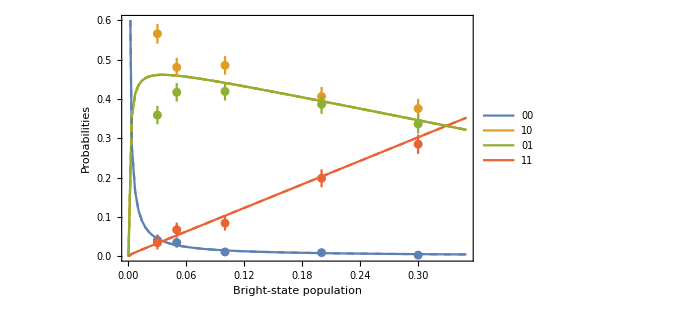

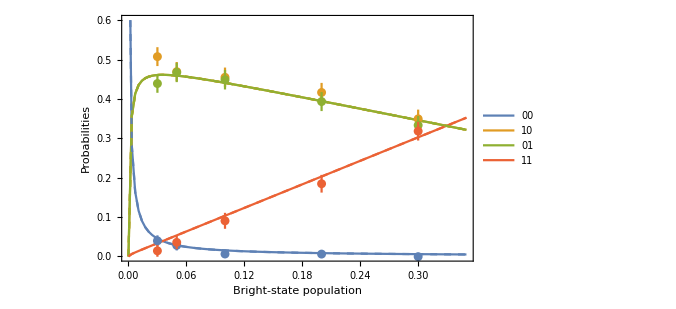

```mathematica
ZZCorrs=ListPlot[CreatePlotLists[GetCorrs,xmin,xmax,100,PhaseErrorRawState[#,setupParams]&,3],Frame->True,PlotRange->{{xmin,xmax},{0,0.6}},FrameLabel->{"Bright-state population","Probabilities"},PlotLegends->{"00","10","01","11"},Joined->True,ImageSize->500];

ZZCorrsb=ListPlot[CreatePlotLists[GetCorrs,xmin,xmax,100,PhaseErrorRawState[#,setupParamsIdeal]&,3],Frame->True,PlotRange->{{xmin,xmax},{0,0.6}},PlotStyle->Dashed,FrameLabel->{"Bright-state population","Probabilities"},Joined->True,ImageSize->500];
ZZCorrsData0=ErrorListPlot[Reverse[CreateDataCorrelatorsPlotLists[Corrs,1,3]],Joined->False];
ZZCorrsData1=ErrorListPlot[Reverse[CreateDataCorrelatorsPlotLists[Corrs,2,3]],Joined->False];

Show[{ZZCorrs,ZZCorrsb,ZZCorrsData0}]
Show[{ZZCorrs,ZZCorrsb,ZZCorrsData1}]
```

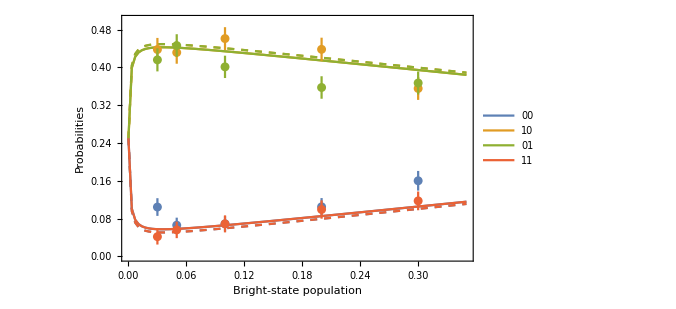

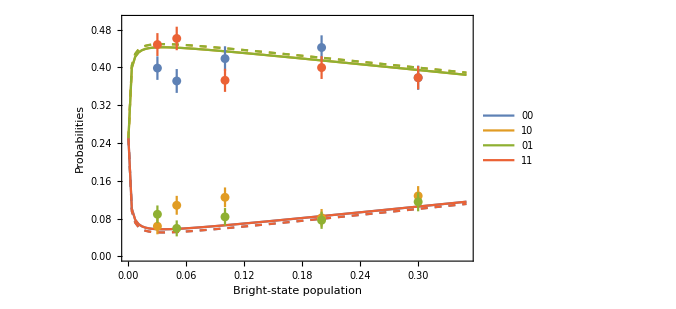

```mathematica
XXCorrs=ListPlot[CreatePlotLists[GetCorrs,xmin,xmax,100,PhaseErrorRawState[#,setupParams]&,2],Frame->True,PlotRange->{{xmin,xmax},{0,0.5}},FrameLabel->{"Bright-state population","Probabilities"},PlotLegends->{"00","10","01","11"},Joined->True,ImageSize->500];

XXCorrsb=ListPlot[CreatePlotLists[GetCorrs,xmin,xmax,100,PhaseErrorRawState[#,setupParamsIdeal]&,2],Frame->True,PlotRange->{{xmin,xmax},{0,0.5}},PlotStyle->Dashed,FrameLabel->{"Bright-state population","Probabilities"},Joined->True,ImageSize->500];

XXCorrsData0=ErrorListPlot[Reverse[CreateDataCorrelatorsPlotLists[Corrs,1,1]],Joined->False];
XXCorrsData1=ErrorListPlot[Reverse[CreateDataCorrelatorsPlotLists[Corrs,2,1]],Joined->False];
Show[{XXCorrs,XXCorrsb,XXCorrsData0}]
Show[{XXCorrs,XXCorrsb,XXCorrsData1}]
```

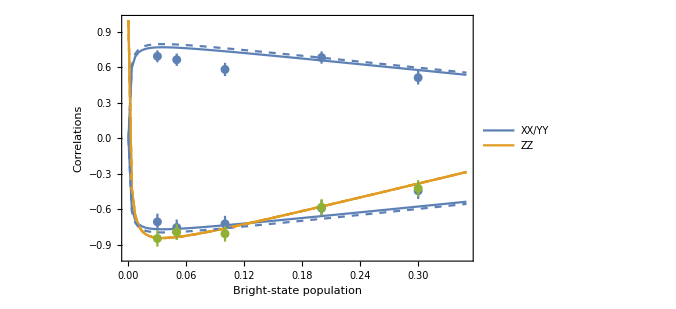

```mathematica
psi0=ListPlot[CreatePlotLists[GetSigmas,xmin,xmax,100,PhaseErrorRawState[#,setupParams]&][[2;;3]],Frame->True,PlotRange->{{xmin,xmax},{-1,1}},FrameLabel->{"Bright-state population","Correlations"},PlotLegends->{"XX/YY","ZZ"},Joined->True,ImageSize->500];

psi1=ListPlot[CreatePlotLists[GetSigmas,xmin,xmax,100,PhaseErrorRawState[#,setupParams,π]&][[2;;3]],Frame->True,PlotRange->{{xmin,xmax},{-1,1}},FrameLabel->{"Bright-state population","Correlations"},Joined->True,ImageSize->500];

psi0b=ListPlot[CreatePlotLists[GetSigmas,xmin,xmax,100,PhaseErrorRawState[#,setupParamsIdeal,0]&][[2;;3]],Frame->True,PlotStyle->Dashed,PlotRange->{{xmin,xmax},{-1,1}},FrameLabel->{"Bright-state population","Correlations"},Joined->True,ImageSize->500];

psi1b=ListPlot[CreatePlotLists[GetSigmas,xmin,xmax,100,PhaseErrorRawState[#,setupParamsIdeal,π]&][[2;;3]],Frame->True,PlotStyle->Dashed,PlotRange->{{xmin,xmax},{-1,1}},FrameLabel->{"Bright-state population","Correlations"},Joined->True,ImageSize->500];

XXCorrDataPsi0=ErrorListPlot[CreateDataCorrelationPlotLists[Corrs,1,1],Joined->False,PlotStyle->{col1,col1}];
XXCorrDataPsi1=ErrorListPlot[CreateDataCorrelationPlotLists[Corrs,2,1],Joined->False,PlotStyle->{col1,col1}];

ZZCorrData=ErrorListPlot[CreateDataCorrelationPlotLists[Corrs,1,3],Joined->False,PlotStyle->{col2,col3}];
Show[{psi0,psi1,psi0b,psi1b,XXCorrDataPsi0,XXCorrDataPsi1,ZZCorrData}]
```

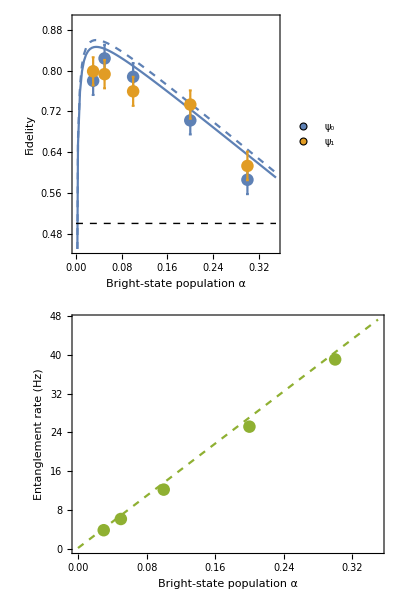

```mathematica
hw = 0.005; (*width of ticks*)
vw= 0.003; (*height of ticks*)
erroBarFunc=Function[{coords,errs},{(*the vertical line:*)Line[{coords-{0,errs[[2,1]]},coords+{0,errs[[2,1]]}}],(*horizontal tick 1:*){Thickness[vw],Line[{coords-{hw/2,-errs[[2,1]]},coords+{hw/2,errs[[2,1]]}}]},(*horizontal tick 2:*){Thickness[vw],Line[{coords-{hw/2,errs[[2,1]]},coords+{hw/2,-errs[[2,1]]}}]}}];


(*pltFidelity = ListPlot[CreatePlotLists[GetFidelities,xmin,xmax,100,PhaseErrorRawState[#,setupParams]&],Frame->{True,True,True,False},PlotStyle->col1,FrameLabel->{"Bright-state population","Fidelity"},FrameStyle->{Automatic,col1,Automatic,Automatic},PlotRange->{Automatic,{0.45,0.9}},Joined->True,ImagePadding->50,ImageSize->500,Epilog->{Directive[Dashed],Line[{{xmin,0.5},{xmax,0.5}}]}];

pltFidelityb = ListPlot[CreatePlotLists[GetFidelities,xmin,xmax,100,PhaseErrorRawState[#,setupParamsIdeal]&],Frame->{True,True,True,False},PlotStyle->Directive[col1,Dashed],FrameLabel->{"Bright-state population","Fidelity"},FrameStyle->{Automatic,col1,Automatic,Automatic},PlotRange->{Automatic,{0.45,0.9}},Joined->True,ImagePadding->50,ImageSize->500];

pltRate = ListPlot[{CreatePlotLists[GetSuccessRate,xmin,xmax,100,setupParams]},Frame->{None,None,None,True},FrameStyle->{{None,col3},{None,None}},FrameLabel->{{"","Entanglement rate (Hz)"},{"",""}},Joined->True,PlotStyle->Directive[Dashed,col3],ImagePadding->50,FrameTicks->{{None,tickFunction},{None,None}},ImageSize->500];

FidData=ErrorListPlot[CreateDataFidelityList[Corrs],Joined->False,ErrorBarFunction->erroBarFunc,PlotStyle->{Directive[PointSize[0.018],col1],Directive[PointSize[0.018],col2]},PlotLegends->Placed[PointLegend[{"ψ_0","ψ_1"},LegendMarkers->{{Graphics[Disk[]],9}},LabelStyle->12,LegendFunction->"Frame"],{0.9,0.6}]];

tailData=ErrorListPlot[CreateDataTailList[Corrs,setupParams["LDEduration"]],ErrorBarFunction->erroBarFunc,PlotStyle->Directive[PointSize[0.018],col3],PlotRange->{{xmin,xmax},Automatic}];

Overlay[{Show[{pltFidelity,pltFidelityb,FidData}],Show[{pltRate,tailData}]}]*)

pltFidelity = ListPlot[CreatePlotLists[GetFidelities,xmin,xmax,100,PhaseErrorRawState[#,setupParams]&],PlotStyle->col1,Frame->True,FrameLabel->{"Bright-state population α","Fidelity"},PlotRange->{Automatic,{0.45,0.9}},Joined->True,ImageSize->500,ImagePadding->{{60,20},{50,60}},Epilog->{Directive[Dashed],Line[{{xmin,0.5},{xmax,0.5}}]}];

pltFidelityb = ListPlot[CreatePlotLists[GetFidelities,xmin,xmax,100,PhaseErrorRawState[#,setupParamsIdeal]&],PlotStyle->Directive[col1,Dashed],Frame->True,FrameLabel->{"Bright-state population α","Fidelity"},PlotRange->{Automatic,{0.45,0.9}},Joined->True,ImageSize->500,ImagePadding->{{60,20},{50,60}}];

pltRate = ListPlot[{CreatePlotLists[GetSuccessRate,xmin,xmax,100,setupParams]},Frame->True,FrameLabel->{"Bright-state population α","Entanglement rate (Hz)"},Joined->True,PlotStyle->Directive[Dashed,col3],ImagePadding->{{60,20},{60,10}},ImageSize->500];

FidData=ErrorListPlot[CreateDataFidelityList[Corrs],Joined->False,ErrorBarFunction->erroBarFunc,PlotStyle->{Directive[PointSize[0.018],col1],Directive[PointSize[0.018],col2]},PlotLegends->Placed[PointLegend[{"ψ_0","ψ_1"},LabelStyle->14,LegendMarkers->{{Graphics[Disk[]],9}}],{0.93,0.86}]];

tailData=ErrorListPlot[CreateDataTailList[Corrs,setupParams["LDEduration"]],ErrorBarFunction->erroBarFunc,PlotStyle->Directive[PointSize[0.018],col3],PlotRange->{{xmin,xmax},Automatic}];
fig = Column[{Show[{pltFidelity,pltFidelityb,FidData}],Show[{pltRate,tailData}]}]
Export["/Users/phumphreys/Repositories/papers/EntOnDemand/paper/Figures/FidAndRates.pdf",fig];
```

#### Sweep XY @ 0.1

```mathematica
SweepPhaseCorrsString =FileNameJoin[{BaseDirString,"LT4_data/EntOnDemand20170705/SweepPhase0p1"}];
SweepPhaseCorrs=GetCorrelationFile["",SweepPhaseCorrsString,True,True,"correlations_2d.h5"];
SweepPhaseCorrs[[1]]=SweepPhaseCorrs[[1]]-SweepPhaseCorrs[[1]][[1]];
```

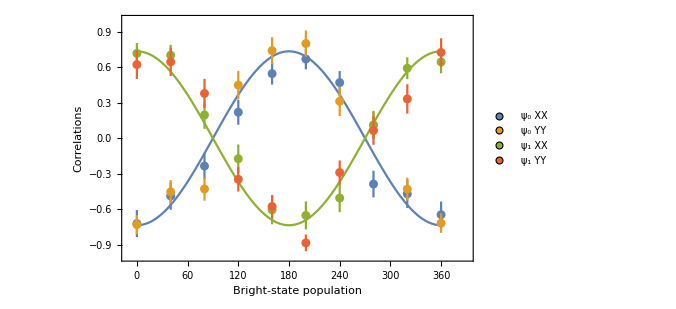

```mathematica
SweepPhaseCorrData=ErrorListPlot[{CreateDataCorrelationPlotLists[SweepPhaseCorrs,1,1],CreateDataCorrelationPlotLists[SweepPhaseCorrs,1,2,True],CreateDataCorrelationPlotLists[SweepPhaseCorrs,2,1],CreateDataCorrelationPlotLists[SweepPhaseCorrs,2,2,True]},Joined->False,PlotStyle->{col1,col2,col3,col4},PlotLegends->Placed[PointLegend[{"ψ_0 XX","ψ_0 YY","ψ_1 XX","ψ_1 YY"},LabelStyle->{14,Background->White},LegendMarkers->{{Graphics[Disk[]],8}}],{0.92,0.5}]];

SweepPhasePsi0=ListPlot[GetRotatedSigmas[0,360,100,PhaseErrorRawState[PopulationToTheta[0.1],setupParams,0]][[1]],Frame->True,PlotStyle->{col1},PlotRange->{{-10,390},{-1,1}},FrameLabel->{"Bright-state population","Correlations"},Joined->True,ImageSize->500];

SweepPhasePsi1=ListPlot[GetRotatedSigmas[0,360,100,PhaseErrorRawState[PopulationToTheta[0.1],setupParams,π]][[1]],Frame->True,PlotStyle->{col3},PlotRange->{{-10,370},{-1,1}},FrameLabel->{"Bright-state population","Correlations"},Joined->True,ImageSize->500];

fig=Show[{SweepPhasePsi0,SweepPhasePsi1,SweepPhaseCorrData}]
Export["/Users/phumphreys/Repositories/papers/EntOnDemand/paper/Figures/SweepPhase0p1.pdf",fig];
```

### SPCorrs sweep theta

```mathematica
(*pDetect1 =0.00014;
pDetect2 = 0.00054;
pDCBothDetect=(0.0072+0.0126)*10^-4;
fracInCorrect1 =(pDCBothDetect(1-pBright))/(pDetect1 pBright+pDCBothDetect);
fracInCorrect2 =(pDCBothDetect(1-pBright))/(pDetect2 pBright+pDCBothDetect);
Plot[{fracInCorrect1,fracInCorrect2},{pBright,0.1,0.5},PlotRange->{Automatic,{0,1}}]*)
```